{-0.245925 ⅇ^(-0.314159 t) (1. ⅇ^(0.314159 t) Cos[6.22035 t]-1. Cos[6.27533 t]-0.201101 ⅇ^(0.314159 t) Sin[6.22035 t]+0.149187 Sin[6.27533 t])}

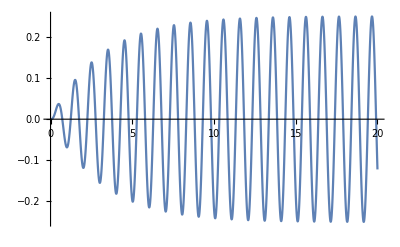

```mathematica
omega0=2*Pi;
omega=0.99*omega0;
gamma=0.1*omega0;
f=Sin[omega*t];
X=x[t]/.DSolve[{x''[t]+gamma*x'[t]+omega0^2*x[t]==f,x[0]==0,x'[0]==0},x,t]
Plot[X,{t,0,20}]
```